# Dynamics of thin liquid films on a porous substrate in zero gravity

## Demonstration of computational solution and visualization Aneet Dharmavaram Narendranath, Lecturer, Michigan Technological University, Houghton, MI, USA

## Objective

Predicting dynamics of liquid films in zero gravity has significant applications for both space travel and terrestrial applications where gravity does not play an important role in comparison with other effects such as surface tension and thermocapillarity (changes in surface tension due to temperature gradients).

A fourth order non - linear partial differential equation (Evolution equation) from the lubrication approximation in fluid dynamics, is applied to study the dynamics of liquid films in zero gravity, under the effect of an interplay between various stabilizing and destabilizing mechanisms.

Long-wave evolution dynamics are compared for two different substrate types: isothermal non-porous and isothermal porous for small Biot number in a zero gravity environment.

The multi-time-scale dynamics is revealed through time scales obtained from a method of similarity solutions. It is observed that with an isothermal porous substrate, in zero gravity, secondary thermocapillary structures are damped through imbibition and that primary thermocapillary structures persist for long times without rupture.

## Fourth Order Non-linear Evolution Equation

```mathematica
-Graphics-
-Graphics-
```

### Terms on LHS:

Stabilizing effect of Surface tension

Stabilizing effect of gravity

Destabilizing effect of thermocapillarity

### Terms on RHS

Stabilizing effect of porous substrate

## Derivation of Evolution Equation

One sided model, lubrication approximation and long wavelength limit [See Narendranath et al. 2014, Burelbach et al. 1988]

### Addition of porous substrate:

Constant pore diameter

No longitudinal imbibition within porous usbstrate

Substrate saturated with the same fluid as the liquid film

Flow within substrate is governed by the Darcy equation

## Simple case: Pendant Drop Formation [isothermal non-porous substrate] Imagine liquid film on ceiling

Package inclusion for solving and postprocessing

```mathematica
Needs["HierarchicalClustering`"]
SetOptions[Plot,ImageSize->Large,PlotStyle->{Black,Thick},BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->24}];
SetOptions[MatrixPlot,ImageSize->Small,BaseStyle->{FontFamily->"SansSerif",Bold}];
SetOptions[ParametricPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->19}];
SetOptions[ListPlot,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold},PlotStyle->{Thick,Black},PlotMarkers->None,Filling->Axis];

$Pre=(SetOptions[EvaluationNotebook[],ShowPredictiveInterface->True];#)&
$Post=Function[expr,If[FreeQ[expr,SparseArray],expr,SetOptions[EvaluationNotebook[],ShowPredictiveInterface->False];expr],HoldAll];

Off[NDSolve::mxsst]
```

(SetOptions[EvaluationNotebook[],ShowPredictiveInterface→True];#1)&

Solution of reduced form of evolution equation

```mathematica
Clear[x,t,xMin, xMax,TMax,frac,m,time];
xMin=0; xMax=2.Pi(Sqrt[2]/1);TMax =80;
   hsol=u /. NDSolve[{D[u[t, x], t] == -D[u[t, x]^3*D[u[t, x], x, x, x], x] - 
        D[u[t, x]^3*D[u[t, x], x], x], u[0, x] == 1 - 0.1*Sin[1*(x/Sqrt[2])], 
      Derivative[0, 1][u][t, xMin] == Derivative[0, 1][u][t, xMax], 
      Derivative[0, 2][u][t, xMin] == Derivative[0, 2][u][t, xMax], 
      Derivative[0, 3][u][t, xMin] == Derivative[0, 3][u][t, xMax], 
      u[t, xMin] == u[t, xMax]}, u, {t, 0, TMax}, {x, xMin, xMax}, 
     MaxStepSize -> 0.1, Method -> "LSODA"][[1]];

Plot[hsol[TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"}];
Manipulate[Plot[hsol[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}}],{time,0,1,0.01}]
```

## The Base case: Surface tension, Thermocapillarity and Gravity

Surface tension and gravity are stabilizing mechanisms while thermocapillary destabilizes the liquid film

Thermocapillary destabilization results in “finger structures” (primary and secondary).

Rupture is defined as that point when the problem is overly stiff to solve and requires a time step of the order of 10^-12.

```mathematica
Clear[x,t,xMin, xMax,TMax,k];
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;k=0.067;
Quiet[hbase= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (1/3)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x], 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbase[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},GridLines->Automatic],{time,0,1,0.05}]]
```

## Zero gravity: Surface tension and thermocapillarity

Gravity is turned “OFF” by ignoring the relevant third order nonlinear term from the evolution equation

```mathematica
Clear[x,t,xMin, xMax,TMax,k];
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;k=0.067;
Quiet[hbase0= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (0/3)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x], 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbase0[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Red},GridLines->Automatic],{time,0,1,0.05}]]
```

## Comparison: Base case vs Zero gravity

Without gravity, film destabilization proceeds quicker and film rupture occurs at an earlier time.

It is also observed that primary and secondary finger structures grow to larger amplitudes without gravity.

```mathematica
TMax=2000.;xMin=-Pi/0.067;xMax=Pi/0.067;
Manipulate[
Plot[{hbase[time TMax,x],hbase0[time TMax,x]},{x,xMin,xMax},PlotRange->{{xMin,xMax},{0,3}},PlotStyle->{{Thick,Black},{Thick,Red}},PlotLegends->{"Base","Zero Gravity"},ImageSize->Medium],
{time,0,1,0.02}]
```

## Base case with porous substrate

When an isothermal porous substrate is introduced, it has the effect of draining the film.

```mathematica
Clear[x,t,xMin, xMax,TMax,k,Pm,mult,Ga];
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;k=0.067;
Pm=0.0025;Ga=1.; mult=1.;
hbasep= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (1./3.)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x]+ mult*Pm*(D[u[t, x], x, x] - Ga*u[t, x]), 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbasep[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Black},GridLines->Automatic],{time,0,1,0.05}]
```

InterpolatingFunction::dmval: Input value {8000., -46.4027} lies outside the range of data in the interpolating function. Extrapolation will be used.

## Effect of porous substrate on film evolving in zero gravity

The porous substrate leads to damping of thermocapillary fingers

The film also avoids rupture for a long duration (Trup≈4 x in case below) of time.  This time of rupture is directly related to porosity (Porous resistance term in Darcy equation).

Multiple phases: Initial evolution similar to base case and zero gravity case on non-porous substrate, intermediate evolution dominated by decceleration of film dynamics and damping of thermocapillary structures, long time film dynamics show arrestation of film dynamics as compared to base case or that with zero gravity.

```mathematica
Clear[x,t,xMin, xMax,TMax,k,Pm,mult,Ga];
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=8000.;k=0.067;
Pm=0.15;Ga=0.; mult=1.;
hbasep0= u /. NDSolve[{D[u[t, x], t] == -100*D[u[t, x]^3*D[u[t, x], x, x, x], x] + 
        (Ga/3.)*D[u[t, x]^3*D[u[t, x], x], x] - 
        5*D[(u[t, x]/(1 + u[t, x]))^2*D[u[t, x], x], x]+ mult*Pm*(D[u[t, x], x, x] - Ga*u[t, x]), 
      u[0, x] == 1 - 0.1*Cos[k*x], u[t, xMin] == u[t, xMax], 
      Derivative[0, 1]*u[t, xMin] == Derivative[0, 1]*u[t, xMax], 
      Derivative[0, 2]*u[t, xMin] == Derivative[0, 2]*u[t, xMax], 
      Derivative[0, 3]*u[t, xMin] == Derivative[0, 3]*u[t, xMax]}, u, {t, 0, TMax}, 
     {x, xMin, xMax}, MaxSteps -> 100000, Method -> {"MethodOfLines", 
       "Method" -> "LSODA", "TemporalVariable" -> t, "SpatialDiscretization" -> 
        {"TensorProductGrid", "MinPoints" -> 800, "MaxPoints" -> 1200, 
         "DifferenceOrder" -> 5}}][[1]];

Manipulate[Plot[hbasep0[time TMax,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Red},GridLines->Automatic],{time,0,1,0.05}]
```

## Comparison of film dynamics of all cases (base, zero gravity, zero gravity with porous substrate)

```mathematica
xMin=-Pi/0.0677; xMax= Pi/0.0677;TMax=2000.;TMaxp=12000.;
Manipulate[
Plot[{hbase[fraction TMax,x],hbase0[fraction TMax,x],hbasep0[fraction TMax,x]},{x,xMin,xMax},PlotStyle->{{Thick,Black},{Thick,Red},{Thick,RGBColor[0.49,0.52,0.36]}},PlotLegends->{"Base case, non porous substrate","Zero Gravity, non porous substrate","Zero Gravity, \bporous substrate\b"},PlotRange->{{xMin,xMax},{0,3.2}},ImageSize->Medium]
,{fraction,0,1,0.02}]
```

All three situations have the same initial conditions and periodic boundary conditions

The case with zero gravity evolution of thermocapillary instabilities on a non porous substrate is the first to rupture at T_rup=2000

The case with zero gravity evolution of thermocapillary instabilities on a porous substrate has not yet ruptured at T_rup=2000.

Initially, the case film on a porous substrate has similar dynamics to the base case (surface tension, gravity, thermocapillarity) and leads leads the latter.

However, the film on a porous substrate experiences a decceleration of film dynamics along with a damping of thermocapillary structures.

## Comparison of film dynamics with Recurrence Plots What is a recurrence plot?

A recurrence plot is a matrix plot of a square matrix that is calculated by the equation:

R_(i,j)=θ(x)(ϵ - Norm[x_i-x_j])

Recurrence plots have so far been applied to study “noise laden” dynamics such as in Medical MRI scans, stock market trends, vibrations of cutting tools etc.

What the recurrence plot equation says is: “Those states that fall into a neighbourhood size ϵ centered at x_i are known to be recurrent”

When a recurrence occurs (such as: revisitation of a trajectory in phase space), ‘1’s are populated in the recurrence matrix R_(i,j)  at the time of the recurrence.  All other positions have ‘0’s.

A traditional RP (recurrence plot) is a “time vs time” plot that shows recurrences at different time intervals (if any).  This leads to tessellations and unique patterns for different (spatio)temporal evolution situations.

### Example of recurrence plot usage

The differential equation: y'(x)==y(x) cos(y(x)+x), with boundary condition y(0)=1 is numerically solved.  The solution shows oscillation and periodicity in x.

The power spectrum of the DFT of y is calculated and compared with the recurrence plot of the same.

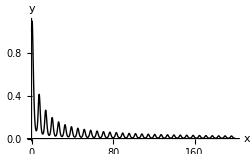

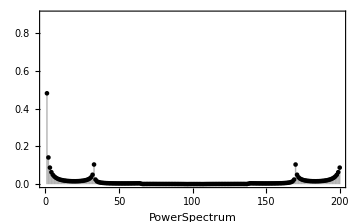

-Graphics-

```mathematica
Clear[ysol,dft,y,x];
ysol=NDSolveValue[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,200}];

dft=Abs[Fourier[Table[ysol[x],{x,0,200,1}]]]^2;
Plot[ysol[x],{x,0,200},ImageSize->250{1,1},BaseStyle->{FontFamily->"SansSerif",FontSize->12},AxesLabel->{"x","y"},PlotRange->{All,{0,1.1}}]
ListPlot[dft[[1;;200]],Filling->Axis,PlotRange->{All,{0,0.9}},ImageSize->Medium,Frame->True,FrameLabel->{"PowerSpectrum",""}]

MatrixPlot[UnitStep[0.0001-DistanceMatrix[ysol[Range[0,200,.2]]]],Frame->True,FrameLabel->{"x","x","Recurrence Plot"},ImageSize->Medium]
```

The recurrence plot shows a tessellated structure that is an aspect of spatial (or temporal) periodic structures.  Qualitatively, changes, removal or addition of frequencies (periodic structures) may be found using RPs.  Analysis algorithms to extract RP data and to study evolutionary time scales is available [Marwan et al.]

## Comparison of film dynamics with Recurrence Plots

Recurrence plots are now used to study film spatiotemporal dynamics

Provides insight on differing times at which periodic structures arise or dissipate.

Zero-g and Base case have a time lag between them.

Zero-g when compared to zero-g+porous substrate show that the floral pattern, indicative of multiple thermocapillary fingers forms in both at around 0.45 T_rup. However, these thermocapillary fingers are held in “suspension” at T_rup with a porous substrate

```mathematica
Manipulate[g11=With[{stepSize=.4,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbase[ fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base \n(Krishnamoorthy et al. 1995)"}]
];
g12=With[{stepSize=0.15,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbase0[fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base + 0g \n(Narendranath et al. 2015)"}]];
g13=With[{stepSize=0.15,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbasep0[fraction TMax,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base + 0g + porosity \n (Narendranath et al. 2016)" }]
];
GraphicsGrid[{{g11,g12,g13}}],{{np,0.,"Time"},0,1,0.05}]
```

## The long time liquid film dynamics with zero gravity and porous substrate damping of thermocapillary structures

This simulation runs for 4 xT_rup(≈8000).

```mathematica
Manipulate[
Plot[hbasep0[np 8000,x],{x,xMin,xMax},AxesLabel->{"Substrate","Film Profile"},PlotRange->{{xMin,xMax},{0,3.}},PlotStyle->{Thick,Red},GridLines->Automatic,ImageSize->Medium,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->12}]

With[{stepSize=.2,end=xMax,fraction=np},
MatrixPlot[UnitStep[0.0001-DistanceMatrix[hbasep0[fraction 8000,Range[xMin,end,stepSize]]]],ColorFunction->"Monochrome",Frame->True,FrameLabel->{"","Base + 0g + porosity \n (Narendranath et al. 2016)" }]
],{{np,0.,"time"},0,1,0.05}]
```

## Multiple time scales : Similarity solution method

The near simultaneous formation of structures and then later time deccelleration, as evidenced from film profile plots and RPs, led to the uncovering of multiple time scales

Another similar study for a “multi time scale situation” on the spreading of droplets on an isothermal substrate (Chowdhury 2015) was discovered, however, our work was carried out independently.

Each physical mechanism and associated non-linear term has a time scale associated with it.  These time scales were found using the method of introducing similarity parameters.  All the non-dimensional numbers were set to be of equal magnitude and the thermocapillarity term was simplified for this preliminary study.

Further study is necessary on what these time scales imply and to find the one-to-one correspondence between various time scales of mechanisms and film dynamics.

It is the presenter’s impression that a coupling between the mechanisms (i.e, the non-linear terms in the evolution equation) needs to be studied.  One avenue is to explore the transformation of this PDE to a non-linear ODE (eg: Blasius Boundary layer equation, non-linear diffusion equations as studied by Huppert et al.)

## Linear Stability and Preliminary Application of Bifurcation Theory

Linear stability analysis is applied to find an expression for growth rate of instabilities and fastest growing wavelength (Similar to Davis et al., Burelbach et al.)

Equation for fastest growing wavelength shows subcritical pitchfork bifurcation (always unstable) for pendant drop case and supercritical pitchfork bifurcation (stability possible) when film is under the influence of TC, SurfTen, Grav, Porous substrate.

The growth rate for LW instabilities is first depicted along with the effect of magnitude of various mechanisms.

Increasing the magnitude of porosity (how porous the substrate is) has a pronounced effect when combined with the effects of gravity and surface tension (Example: M:S and M:G are 5:1., when M:Pm::5:0.5, every 0.5 increase in Porosity reduces growth rate of instabilities by approximately 10%.

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm,qmaxval];
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn;
Bi=0.1;
qmaxval=2;
Manipulate[Plot[f/.{Ga->xg 1.,Sn->xs 100.,Pm->xp 1/2,M->xm 5.},{q,0,qmaxval},PlotRange->{{0,qmaxval},{0,8}},BaseStyle->{FontSize->18},PlotStyle->{Thick,Black},ImageSize->Large,GridLines->Automatic,Frame->True,FrameLabel->{"wavenumber \n(inverse wavelength)","Growth rate"}],{{xg,0.,"Gravity"},0,10},{{xs,.6,"Surf Ten"},0.1,1},{{xp,0.,"Porosity"},0,10},{{xm,5,"ThermoCap."},0,5}]
```

## Bifurcation Plots ...”Two roads diverged in a yellow wood, And sorry I could not travel both” {Robert Frost, 1916}

The equation for determining fastest growing wavenumber is found to resemble:

-Graphics-

This is the archetypical equation that represents supercritical pitchfork bifurcation

In this equation, μ is a balance between various non dimensional numbers in the evolution equation. The wavenumber is denoted by “x”.  Typical values for M, Bi, Ga and Sn are chosen.  Pm is “free” and may change the effect of the parameter, μ.  In theory, μ may be changed with any combination of non-dim numbers.

-Graphics-

```mathematica
Clear[f,Ga,Sn,Bi,M,q,Pm,μ];
Bi=0.1;M=5.;
Ga=1.;Sn=100.;
Print["Growth rate (f) equation: "]
f=-(Ga q^2)/3+(M q^2)/(1+Bi)^2+Pm (-Ga-q^2)-q^4 Sn
df=Collect[D[f/(4 Sn),q],q]
df2=df/.q->x
df3=df2/.(0.0025 (7.5977961432506875-2 Pm))->μ
```

Growth rate (f) equation:

3.7989 q^2-100. q^4+Pm (-1.-q^2)

0.0025 (7.5978-2 Pm) q-1. q^3

0.0025 (7.5978-2 Pm) x-1. x^3

-1. x^3+x μ

{x→0.,x→-1. √μ,x→√μ}

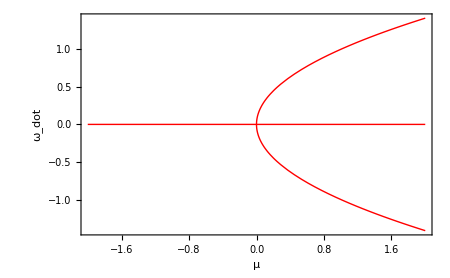

```mathematica
Clear[roots,x];
roots=Quiet[Solve[df3==0,x]//Flatten]
Plot[{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]},{μ,-2,2},PlotStyle->{{Thick,Red},{Thick,Red},{Thick,Red}},ImageSize->450{1,1},FrameLabel->{"μ","ω_dot"(*, "Supercritical Pitchfork Bifurcation \n as demonstrated by eqn for fastest growing wavenumber"*)},Frame->True,BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->14}]
```

## Bifurcation Plots ... and potentials, attractors and repellors

Defining a potential as per Drazin, Strogatz (ω_dot is the equation for maximizing wavenumber)

It is found that the attractors of the potential are those wavenumbers (and hence wavelengths) that lead to maximum growth rates of LW instabilities.

0.25 x^4-(x^2 μ)/2

{0.,-1. √μ,√μ}

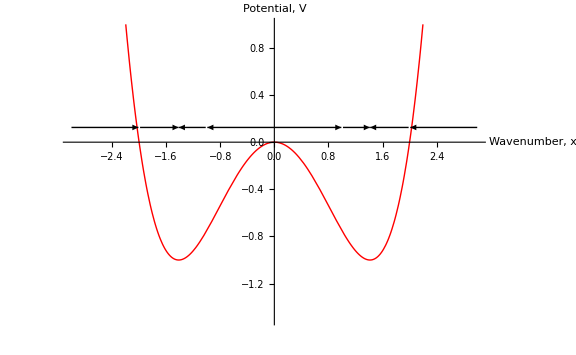

```mathematica
Clear[f,μ,x,λ,roots,GaMin,GaMax,xmin,xmax,ymin,ymax,Ga,Sn];
V=Collect[-Integrate[df3,x],x^2]
roots=Quiet[Solve[df3==0,x]]//Flatten;
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]}
μ=2.;
Show[
Plot[V,{x,-3,3},PlotStyle->{Thick,Red},PlotRange->{{-3,3},{-1.5,1}},AxesLabel->{"Wavenumber, x","Potential, V"},BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->14}],
StreamPlot[{df3,0.},{x,-3,3},{y,0,0.25},GridLines->Automatic,StreamScale->Medium,StreamStyle->{Thick,Black}]
]
```

All roads lead to the attractor.

0.25 x^4-(x^2 μ)/2

{0.,-1. √μ,√μ}

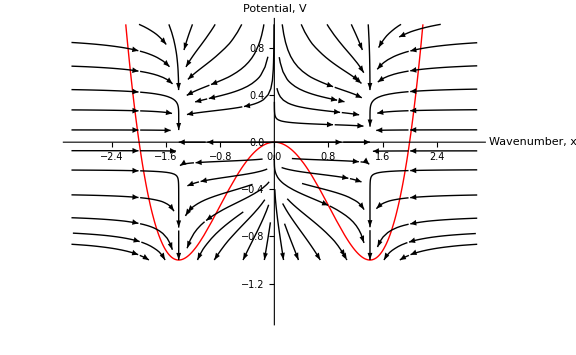

```mathematica
Clear[f,μ,x,λ,roots,GaMin,GaMax,xmin,xmax,ymin,ymax,Ga,Sn];
V=Collect[-Integrate[df3,x],x^2]
roots=Quiet[Solve[df3==0,x]]//Flatten;
{roots[[1]][[2]],roots[[2]][[2]],roots[[3]][[2]]}
μ=2.;
Show[
Plot[V,{x,-3,3},PlotStyle->{Thick,Red},PlotRange->{{-3,3},{-1.5,1}},AxesLabel->{"Wavenumber, x","Potential, V"},BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->14},ImageSize->Large],
StreamPlot[{df3,-y^2},{x,-3,3},{y,-1,1},GridLines->Automatic,StreamScale->Medium,StreamStyle->{Thin,Black}]
]
```

## Connection between Growth rate of LW instabilities and the Duffing Oscillator

{x1→-1,x1→0,x1→1}

-x1^2/2+x1^4/4

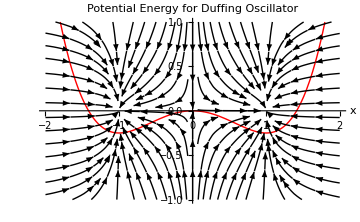

```mathematica
f1=x2;f2=x1-x1^3;
Quiet[Solve[f2==0,x1]]//Flatten
Vx1=-Integrate[f2,x1]
Show[Plot[{Vx1},{x1,-2,2},PlotRange->{All,{-1,1}},PlotStyle->{{Thick,Red}},ImageSize->Medium,AxesLabel->{"x","Potential Energy for Duffing Oscillator"},BaseStyle->{FontFamily->"SansSerif",Bold,FontSize->14}],
StreamPlot[{f2,-f1},{x1,-2,2},{x2,-1,1},StreamStyle->{Thin,Black}]]
```

## Bibliography

Burelbach, James P., Seymour G.Bankoff, and Stephen H.Davis."Nonlinear stability of evaporating/condensing liquid films." Journal of Fluid Mechanics 195 (1988) : 463 - 494.

Williams, Malcolm B., and Stephen H. Davis. “Nonlinear theory of film rupture.” Journal of Colloid and Interface Science 90, no. 1 (1982): 220-228.

Narendranath, Aneet D., James C. Hermanson, Robert W. Kolkka, Allan A. Struthers, and Jeffrey S. Allen. “The Effect of Gravity on the Stability of an Evaporating Liquid Film.” Microgravity Science and Technology 26, no. 3 (2014): 189-199.

Narendranath, Aneet Dharmavaram. “Dynamics of thin liquid films on a porous substrate in zero gravity.” arXiv preprint arXiv:1605.08173 (2016).

Strogatz, Steven H. Nonlinear dynamics and chaos: with applications to physics, biology, chemistry, and engineering. Westview press, 2014.

Drazin, Philip G. Nonlinear systems. Vol. 10. Cambridge University Press, 1992.

Marwan, Norbert, M. Carmen Romano, Marco Thiel, and Jürgen Kurths. “Recurrence plots for the analysis of complex systems.” Physics reports 438, no. 5 (2007): 237-329.